```mathematica
H[k_]:=d0[k]*PauliMatrix[0]+d1[k]*PauliMatrix[1]+d2[k]*PauliMatrix[2]+d3[k]*PauliMatrix[3]
Table[1/2Tr[H[k].PauliMatrix[i]]//FullSimplify,{i,0,3}]
Table[1/2Tr[MatrixExp[ⅈ*H[k]].PauliMatrix[i]]//FullSimplify,{i,0,3}]
```

{d0[k],d1[k],d2[k],d3[k]}

{ⅇ^(ⅈ d0[k]) Cos[√(d1[k]^2+d2[k]^2+d3[k]^2)],(ⅈ ⅇ^(ⅈ d0[k]) d1[k] Sin[√(d1[k]^2+d2[k]^2+d3[k]^2)])/(√(d1[k]^2+d2[k]^2+d3[k]^2)),(ⅈ ⅇ^(ⅈ d0[k]) d2[k] Sin[√(d1[k]^2+d2[k]^2+d3[k]^2)])/(√(d1[k]^2+d2[k]^2+d3[k]^2)),(ⅈ ⅇ^(ⅈ d0[k]) d3[k] Sin[√(d1[k]^2+d2[k]^2+d3[k]^2)])/(√(d1[k]^2+d2[k]^2+d3[k]^2))}

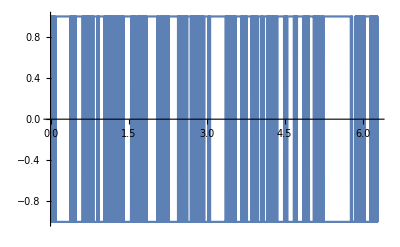

```mathematica
H[k_]:=Cos[k]*PauliMatrix[1]+Sin[k]*PauliMatrix[2]
Plot[Im[Log[Eigenvalues[MatrixExp[ⅈ*H[k]]]]],{k,0,2π},PlotRange->Full]
```